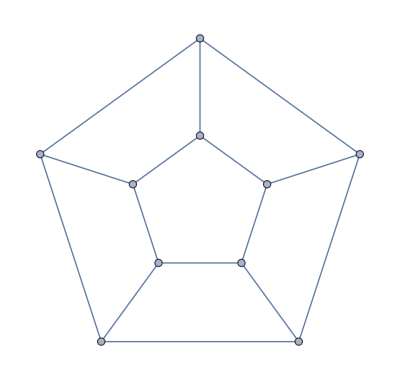

```mathematica
g=Graph[{1<-> 2,2<->3,3<->4,4<->5,5<->1,1<->6,2<->7,3<->8,4<->9,5<->10,6<->7,7<->8,8<->9,9<->10,10<->6}, GraphLayout->"TutteEmbedding"]
```

```mathematica
emb=GraphEmbedding[g]
```

{{-1.83697×10^-16,1.},{-0.951057,0.309017},{-0.587785,-0.809017},{0.587785,-0.809017},{0.951057,0.309017},{-8.76402×10^-6,0.419826},{-0.399281,0.129736},{-0.246771,-0.339639},{0.246759,-0.339639},{0.399269,0.129735}}

```mathematica
emb2=Table[VertexList[g][[k]]->emb[[k]],{k,VertexCount[g]}]
```

{1→{-1.83697×10^-16,1.},2→{-0.951057,0.309017},3→{-0.587785,-0.809017},4→{0.587785,-0.809017},5→{0.951057,0.309017},6→{-8.76402×10^-6,0.419826},7→{-0.399281,0.129736},8→{-0.246771,-0.339639},9→{0.246759,-0.339639},10→{0.399269,0.129735}}

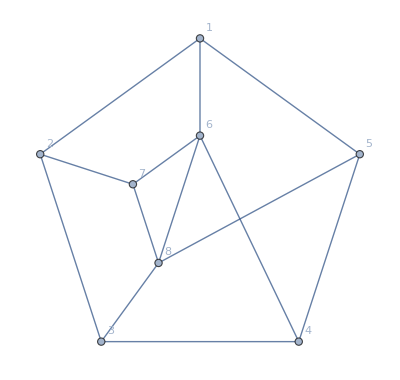

```mathematica
Graph[VertexContract[VertexContract[g,{6,9}],{8,10}], VertexCoordinates->Select[emb2,!MemberQ[{9,10},#[[1]]]&],VertexLabels->"Name"]
```

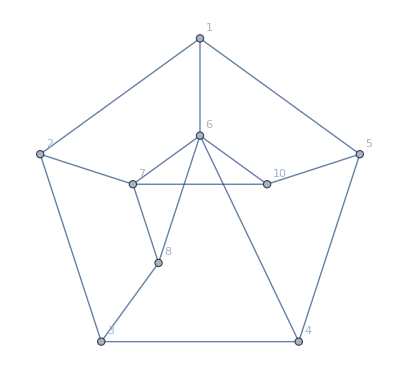

```mathematica
Graph[EdgeAdd[VertexContract[Graph[{6<->7,7<->8,8<->9,9<->10,10<->6,1<-> 2,2<->3,3<->4,4<->5,5<->1,1<->6,2<->7,3<->8,4<->9,5<->10}],{6,9}],7<->10], VertexCoordinates->Select[emb2,!MemberQ[{9},#[[1]]]&],VertexLabels->"Name"]
```

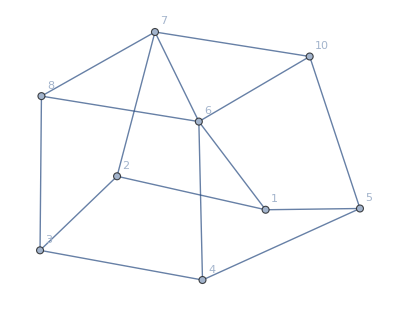

```mathematica
Graph[EdgeAdd[VertexContract[Graph[{6<->7,7<->8,8<->9,9<->10,10<->6,1<-> 2,2<->3,3<->4,4<->5,5<->1,1<->6,2<->7,3<->8,4<->9,5<->10}],{6,9}],7<->10],VertexLabels->"Name"]
```

## second attempt

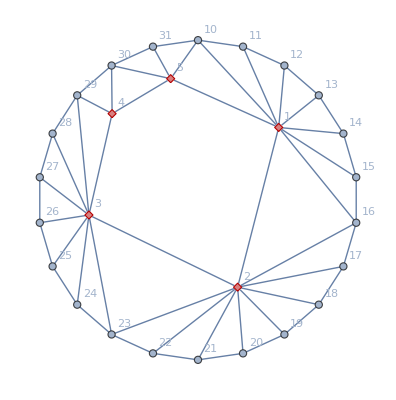

```mathematica
h=Graph[Join[{1<-> 2,2<->3,3<->4,4<->5,5<->1},Table[k<->k+1,{k,10,30}],{31<->10,5<->10},Table[1<->k,{k,10,16}],Table[2<->k,{k,16,23}],Table[3<->k,{k,23,29}],Table[4<->k,{k,29,30}],Table[5<->k,{k,30,31}]], GraphLayout->"TutteEmbedding"];Graph[h,VertexLabels->"Name",GraphHighlight->{1,2,3,4,5},GraphHighlightStyle->"VertexDiamond"]
```

```mathematica
emb=GraphEmbedding[h]
```

{{0.504912,0.45384},{0.247782,-0.545429},{-0.682298,-0.0940476},{-0.537416,0.540259},{-0.170975,0.758969},{-1.83697×10^-16,1.},{0.281733,0.959493},{0.540641,0.841254},{0.75575,0.654861},{0.909632,0.415415},{0.989821,0.142315},{0.989821,-0.142315},{0.909632,-0.415415},{0.75575,-0.654861},{0.540641,-0.841254},{0.281733,-0.959493},{6.12323×10^-17,-1.},{-0.281733,-0.959493},{-0.540641,-0.841254},{-0.75575,-0.654861},{-0.909632,-0.415415},{-0.989821,-0.142315},{-0.989821,0.142315},{-0.909632,0.415415},{-0.75575,0.654861},{-0.540641,0.841254},{-0.281733,0.959493}}

```mathematica
emb2=Table[VertexList[h][[k]]->emb[[k]],{k,VertexCount[h]}]
```

{1→{0.504912,0.45384},2→{0.247782,-0.545429},3→{-0.682298,-0.0940476},4→{-0.537416,0.540259},5→{-0.170975,0.758969},10→{-1.83697×10^-16,1.},11→{0.281733,0.959493},12→{0.540641,0.841254},13→{0.75575,0.654861},14→{0.909632,0.415415},15→{0.989821,0.142315},16→{0.989821,-0.142315},17→{0.909632,-0.415415},18→{0.75575,-0.654861},19→{0.540641,-0.841254},20→{0.281733,-0.959493},21→{6.12323×10^-17,-1.},22→{-0.281733,-0.959493},23→{-0.540641,-0.841254},24→{-0.75575,-0.654861},25→{-0.909632,-0.415415},26→{-0.989821,-0.142315},27→{-0.989821,0.142315},28→{-0.909632,0.415415},29→{-0.75575,0.654861},30→{-0.540641,0.841254},31→{-0.281733,0.959493}}

```mathematica
Graph[h,VertexCoordinates->emb2,VertexCoordinates->emb2,VertexLabels->"Name",GraphHighlight->{1,2,3,4,5},GraphHighlightStyle->"VertexDiamond"]
```

-Graphics-

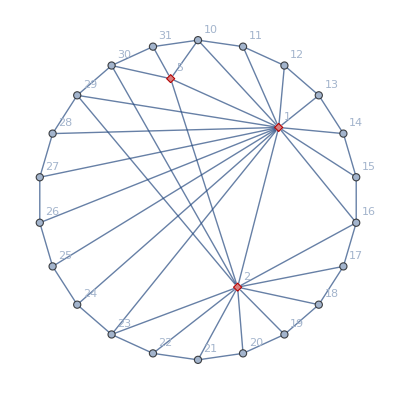

```mathematica
Graph[VertexContract[VertexContract[h,{1,3}],{2,4}],VertexCoordinates->emb2,VertexLabels->"Name",GraphHighlight->{1,2,3,4,5},GraphHighlightStyle->"VertexDiamond"]
```

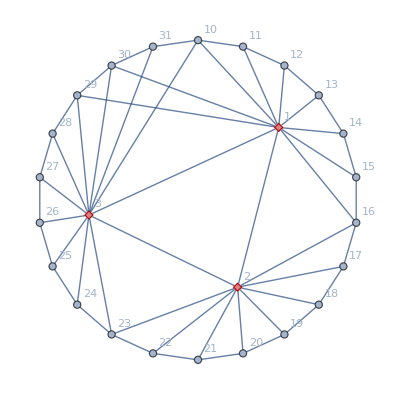

```mathematica
Graph[VertexContract[VertexContract[h,{1,4}],{3,5}],VertexCoordinates->emb2,VertexLabels->"Name",GraphHighlight->{1,2,3,4,5},GraphHighlightStyle->"VertexDiamond"]
```

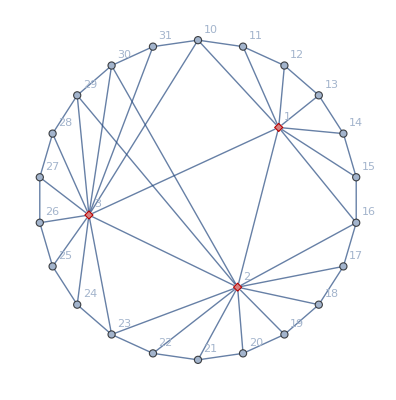

```mathematica
Graph[VertexContract[VertexContract[h,{2,4}],{3,5}],VertexCoordinates->emb2,VertexLabels->"Name",GraphHighlight->{1,2,3,4,5},GraphHighlightStyle->"VertexDiamond"]
```

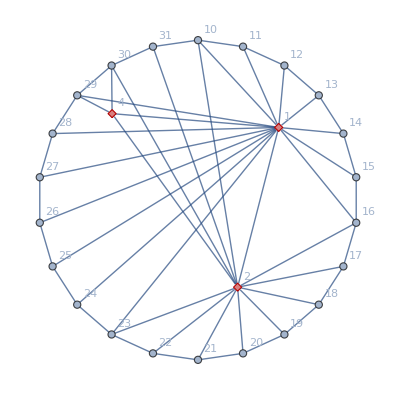

```mathematica
Graph[VertexContract[VertexContract[h,{1,3}],{2,5}],VertexCoordinates->emb2,VertexLabels->"Name",GraphHighlight->{1,2,3,4,5},GraphHighlightStyle->"VertexDiamond"]
```

```mathematica
Graph[VertexContract[VertexContract[h,{1,4}],{3,5}],VertexCoordinates->emb2,VertexLabels->"Name",GraphHighlight->{1,2,3,4,5},GraphHighlightStyle->"VertexDiamond"]
```

-Graphics-

```mathematica
Table[allGraphs[k,"graph"],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[allGraphs[k,"graph"],{k,{quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

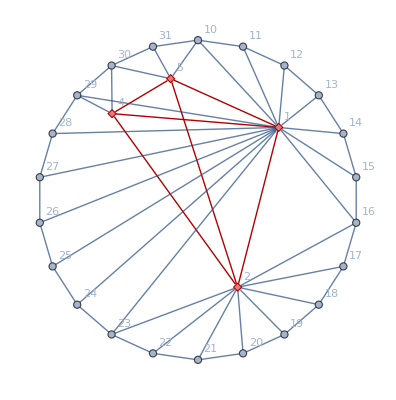

```mathematica
Graph[EdgeAdd[VertexContract[h,{1,3}],{2<->5,4<->2}],VertexCoordinates->emb2,VertexCoordinates->emb2,VertexLabels->"Name",GraphHighlight->{1,2,3,4,5,1<->5,4<->5,1<->4,4<->2,1<->2,2<->5},GraphHighlightStyle->"VertexDiamond"]
```

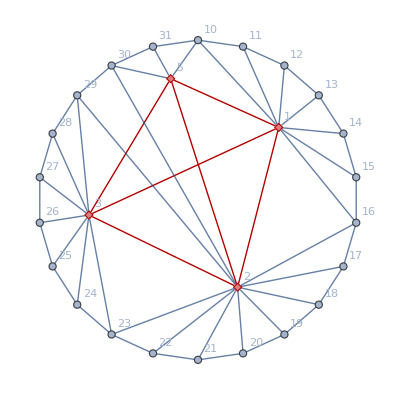

```mathematica
Graph[EdgeAdd[VertexContract[h,{2,4}],{3<->5,1<->3}],VertexCoordinates->emb2,VertexCoordinates->emb2,VertexLabels->"Name",GraphHighlight->{1,2,3,4,5,1<->5,4<->5,1<->4,4<->2,1<->2,2<->5,3<->5,2<->3,1<->3},GraphHighlightStyle->"VertexDiamond"]
```

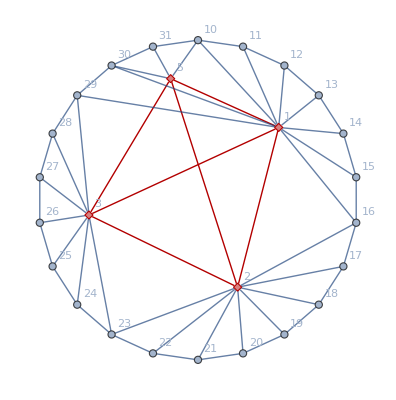

```mathematica
Graph[EdgeAdd[VertexContract[h,{1,4}],{2<->5,3<->5}],VertexCoordinates->emb2,VertexCoordinates->emb2,VertexLabels->"Name",GraphHighlight->{1,2,3,4,5,1<->5,4<->5,1<->4,4<->2,1<->2,2<->5,3<->5,2<->3,1<->3,3<->4},GraphHighlightStyle->"VertexDiamond"]
```

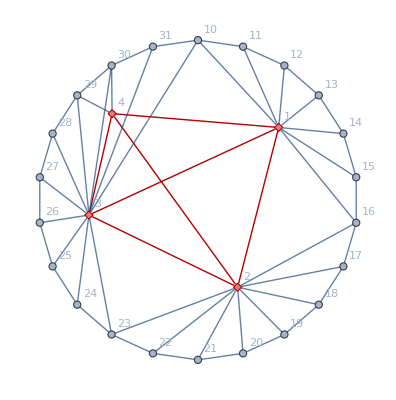

```mathematica
Graph[EdgeAdd[VertexContract[h,{3,5}],{4<->2,4<->1}],VertexCoordinates->emb2,VertexCoordinates->emb2,VertexLabels->"Name",GraphHighlight->{1,2,3,4,5,1<->5,4<->5,1<->4,4<->2,1<->2,2<->5,3<->5,2<->3,1<->3,3<->4},GraphHighlightStyle->"VertexDiamond"]
```

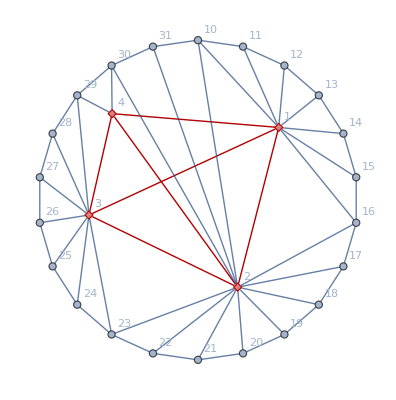

```mathematica
Graph[EdgeAdd[VertexContract[h,{2,5}],{3<->1,1<->4}],VertexCoordinates->emb2,VertexCoordinates->emb2,VertexLabels->"Name",GraphHighlight->{1,2,3,4,5,1<->5,4<->5,1<->4,4<->2,1<->2,2<->5,3<->5,2<->3,1<->3,3<->4},GraphHighlightStyle->"VertexDiamond"]
```